# Vaje iz Mathematice, 2. del

### 1. naloga:

Izračunaj vrednost izraza  30! -20! +110

```mathematica
n := 30! - 20! + 110
n
```

265252859812188625734300303360110

```mathematica
265252859812188625734300303360110
```

265252859812188625734300303360110

Kakšna je 10. števka od leve proti desni?

```mathematica
RealDigits[n][[1]][[10]]
```

8

Rezultat razcepi na prafaktorje.

```mathematica
FactorInteger[n]
```

{{2,1},{5,1},{11,3},{41,1},{101,1},{897840721,1},{5360156751159421,1}}

Katero je največje praštevilo v razcepu?

```mathematica
Max[FactorInteger[n]]
```

5360156751159421

Katero praštevilo nastopa v razcepu z najvišjo potenco?

```mathematica
First[MaximalBy[FactorInteger[n], Last]  ] // First
```

11

```mathematica
SortBy[FactorInteger[n], Max[Last]]  // Last // First
```

11

### 2. naloga:

Poišči vse delitelje števila 16524000.

```mathematica
ClearAll[m]
m := 16524000
```

```mathematica
Divisors[m]
```

{1,2,3,4,5,6,8,9,10,12,15,16,17,18,20,24,25,27,30,32,34,36,40,45,48,50,51,54,60,68,72,75,80,81,85,90,96,100,102,108,120,125,135,136,144,150,153,160,162,170,180,200,204,216,225,240,243,250,255,270,272,288,300,306,324,340,360,375,400,405,408,425,432,450,459,480,486,500,510,540,544,600,612,648,675,680,720,750,765,800,810,816,850,864,900,918,972,1000,1020,1080,1125,1200,1215,1224,1275,1296,1350,1360,1377,1440,1500,1530,1620,1632,1700,1800,1836,1944,2000,2025,2040,2125,2160,2250,2295,2400,2430,2448,2550,2592,2700,2720,2754,3000,3060,3240,3375,3400,3600,3672,3825,3888,4000,4050,4080,4131,4250,4320,4500,4590,4860,4896,5100,5400,5508,6000,6075,6120,6375,6480,6750,6800,6885,7200,7344,7650,7776,8100,8160,8262,8500,9000,9180,9720,10125,10200,10800,11016,11475,12000,12150,12240,12750,12960,13500,13600,13770,14688,15300,16200,16524,17000,18000,18360,19125,19440,20250,20400,20655,21600,22032,22950,24300,24480,25500,27000,27540,30375,30600,32400,33048,34000,34425,36000,36720,38250,38880,40500,40800,41310,44064,45900,48600,51000,54000,55080,57375,60750,61200,64800,66096,68000,68850,73440,76500,81000,82620,91800,97200,102000,103275,108000,110160,114750,121500,122400,132192,137700,153000,162000,165240,172125,183600,194400,204000,206550,220320,229500,243000,275400,306000,324000,330480,344250,367200,413100,459000,486000,516375,550800,612000,660960,688500,826200,918000,972000,1032750,1101600,1377000,1652400,1836000,2065500,2754000,3304800,4131000,5508000,8262000,16524000}

Katera od njih so praštevila?

```mathematica
Select[Divisors[m], PrimeQ]
```

{2,3,5,17}

```mathematica
FactorInteger[m]
```

{{2,5},{3,5},{5,3},{17,1}}

S kakšnimi potencami nastopajo v razcepu števila 16524000?

```mathematica
Table[Last[i],{i,FactorInteger[m]}]
```

FactorInteger::exact: Argument m in FactorInteger[m] is not an exact number.

Table::iterb: Iterator {i,FactorInteger[m]} does not have appropriate bounds.

Table[Last[i],{i,FactorInteger[m]}]

### 3. naloga:

Izračunaj  lim_(x→2) (x^3-4 x^2+2x+4)/(x^5-9x-14)

```mathematica
lim_(x->2) (x^3-4 x^2+2x+4)/(x^5-9x-14)
```

-2/71

```mathematica
Limit[(x^3-4x^2+2x+4)/(x^5-9x-14), x-> 2]
```

-2/71

Izračunaj  lim_(x→0) (arctg (7x))/(arcsin (8x))

```mathematica
Limit[ArcTan[7x],x-> 0]
Limit[ArcSin[8x],x->0]
```

0

0

```mathematica
ClearAll[x]
Limit[ArcTan[7x]/ArcSin[8x], x->0]
```

7/8

Izračunaj  lim_(x→5) (x^2-25)ctg (π x)

```mathematica
Limit[(x^2-25)Cot[πx],x->5]
```

0

Izračunaj  lim_(x→π) (1+cos x)/(2 √(π x)-π-x)

```mathematica
Limit[(1+Cos[x])/(2 √(π x)-π-x), x-> π]
```

-2 π

Izračunaj levo limito:  lim_(x→0^-) |x|ctg x

```mathematica
Limit[Abs[x]Cot[x], x->0, Direction->"FromAbove"]
```

1

Izračunaj desno limito:  lim_(x→0^+) |x|ctg x

```mathematica
Limit[Abs[x]Cot[x], x->0, Direction->"FromBelow"]
```

-1

### 4. naloga:

Izračunaj prvi odvod funkcije  y=2sin (2x+1)  cos (x)

```mathematica
f[x_] := 2Sin[2x+1]Cos[x]
f'[x]
```

4 Cos[x] Cos[1+2 x]-2 Sin[x] Sin[1+2 x]

Izračunaj prvi odvod funkcije  y=x ln (2x)

```mathematica
f[x_]:=x Log[2x]
f'[x]
```

1+Log[2 x]

Izračunaj prvi odvod funkcije  y=(3x-2)^(1/3)/(√(2x+1))

```mathematica
f[x_] := (2x-2)^(1/3)/(√(2x+1))
f'[x] // Simplify
```

-(2^(1/3) (-4+x))/(3 (-1+x)^(2/3) (1+2 x)^(3/2))

Izračunaj drugi odvod funkcije  y=(x+1)^x

```mathematica
f[x_] := (x+1)^x
f''[x]
```

(1+x)^x (-x/(1+x)^2+2/(1+x))+(1+x)^x (x/(1+x)+Log[1+x])^2

### 5. naloga:

Numerično izračunaj ničle polinoma  x^7-2 x^6-x^5-2 x^4+12 x^2-x+1.

```mathematica
roots = Roots[x^7 - 2x^6-x^5-2x^4+12x^2-x+1 == 0, x]
```

x==Root-1.38Root[1-#1+12 #1^2-2 #1^4-#1^5-2 #1^6+#1^7&,1]-1.3752699335115919||x==Root1.59Root[1-#1+12 #1^2-2 #1^4-#1^5-2 #1^6+#1^7&,2]1.5949411250735304||x==Root2.41Root[1-#1+12 #1^2-2 #1^4-#1^5-2 #1^6+#1^7&,3]2.4108595453371398||x==Root-0.356-1.47 ⅈRoot[1-#1+12 #1^2-2 #1^4-#1^5-2 #1^6+#1^7&,4]-0.3562064041542111||x==Root-0.356+1.47 ⅈRoot[1-#1+12 #1^2-2 #1^4-#1^5-2 #1^6+#1^7&,5]-0.3562064041542111||x==Root0.0409-0.284 ⅈRoot[1-#1+12 #1^2-2 #1^4-#1^5-2 #1^6+#1^7&,6]0.040941035704671946||x==Root0.0409+0.284 ⅈRoot[1-#1+12 #1^2-2 #1^4-#1^5-2 #1^6+#1^7&,7]0.040941035704671946

```mathematica
p = x^7 - 2x^6-x^5-2x^4+12x^2-x+1 
x /. NSolve[p==0]
```

1-x+12 x^2-2 x^4-x^5-2 x^6+x^7

{-1.37527,-0.356206-1.47367 ⅈ,-0.356206+1.47367 ⅈ,0.040941-0.283889 ⅈ,0.040941+0.283889 ⅈ,1.59494,2.41086}

Katere od teh ničel so realne?

```mathematica
Select[{-1.3752699335115919,-0.35620640415421095-1.473665610992324 ⅈ,-0.35620640415421095+1.473665610992324 ⅈ,0.040941035704671946-0.28388906750905923 ⅈ,0.040941035704671946+0.28388906750905923 ⅈ,1.5949411250735304,2.4108595453371398}, RealQ]
```

{-1.37527,1.59494,2.41086}

Kakšna je največja absolutna vrednost ničle?

```mathematica
Max[Abs[{-1.3752699335115919,-0.35620640415421095-1.473665610992324 ⅈ,-0.35620640415421095+1.473665610992324 ⅈ,0.040941035704671946-0.28388906750905923 ⅈ,0.040941035704671946+0.28388906750905923 ⅈ,1.5949411250735304,2.4108595453371398}]]
```

2.41086

### 6. naloga:

Razcepi polinom  x^7+2 x^6-80 x^5+232 x^4+175 x^3-826 x^2+256x-1056  na linearne in kvadratne faktorje.

```mathematica
q =  x^7+2 x^6-80 x^5+232 x^4+175 x^3-826 x^2+256x-1056
```

-1056+256 x-826 x^2+175 x^3+232 x^4-80 x^5+2 x^6+x^7

```mathematica
Factor[q]
```

(-4+x)^2 (-3+x) (2+x) (11+x) (1+x^2)

Razcepi isti polinom na linearne faktorje.

```mathematica
Factor[q, Extension->{Sqrt[2], I, 2I, 2}]
```

(-4+x)^2 (-3+x) (-ⅈ+x) (ⅈ+x) (2+x) (11+x)

Faktoriziraj trigonometrični izraz  sin (x)+cos (2x)

Factor::nalg: ⅇ^ⅈ is not an explicit algebraic number.

```mathematica
Factor[Cos[2 x]+Sin[x], Trig-> True] // Simplify
```

1+Sin[x]-2 Sin[x]^2

### 7. naloga:

Definiraj polinom  (x^2 (y-1)-x^3 y^5+(x-1)^7 x y (x^2+2x y+y^3))^2  kot novo spremenljivko.

```mathematica
pipi = (x^2 (y-1)-x^3 y^5+(x-1)^7 x y (x^2+2x y+y^3))^2
```

(x^2 (-1+y)-x^3 y^5+(-1+x)^7 x y (x^2+2 x y+y^3))^2

Razširi polinom tako, da dobiš vsoto monomov.

```mathematica
Expand[pipi]
```

x^4-2 x^4 y+2 x^5 y-14 x^6 y+42 x^7 y-70 x^8 y+70 x^9 y-42 x^10 y+14 x^11 y-2 x^12 y+5 x^4 y^2-30 x^5 y^2+99 x^6 y^2-196 x^7 y^2+301 x^8 y^2-518 x^9 y^2+1071 x^10 y^2-2020 x^11 y^2+3005 x^12 y^2-3432 x^13 y^2+3003 x^14 y^2-2002 x^15 y^2+1001 x^16 y^2-364 x^17 y^2+91 x^18 y^2-14 x^19 y^2+x^20 y^2-4 x^4 y^3+32 x^5 y^3-140 x^6 y^3+504 x^7 y^3-1596 x^8 y^3+4088 x^9 y^3-8036 x^10 y^3+12016 x^11 y^3-13728 x^12 y^3+12012 x^13 y^3-8008 x^14 y^3+4004 x^15 y^3-1456 x^16 y^3+364 x^17 y^3-56 x^18 y^3+4 x^19 y^3+2 x^3 y^4-10 x^4 y^4-14 x^5 y^4+294 x^6 y^4-1386 x^7 y^4+3962 x^8 y^4-7994 x^9 y^4+12010 x^10 y^4-13728 x^11 y^4+12012 x^12 y^4-8008 x^13 y^4+4004 x^14 y^4-1456 x^15 y^4+364 x^16 y^4-56 x^17 y^4+4 x^18 y^4-2 x^3 y^5+16 x^4 y^5-68 x^5 y^5+252 x^6 y^5-798 x^7 y^5+2044 x^8 y^5-4018 x^9 y^5+6008 x^10 y^5-6864 x^11 y^5+6006 x^12 y^5-4004 x^13 y^5+2002 x^14 y^5-728 x^15 y^5+182 x^16 y^5-28 x^17 y^5+2 x^18 y^5+4 x^3 y^6-56 x^4 y^6+362 x^5 y^6-1454 x^6 y^6+3990 x^7 y^6-7966 x^8 y^6+11942 x^9 y^6-13658 x^10 y^6+11970 x^11 y^6-7994 x^12 y^6+4002 x^13 y^6-1456 x^14 y^6+364 x^15 y^6-56 x^16 y^6+4 x^17 y^6+4 x^5 y^7-28 x^6 y^7+84 x^7 y^7-140 x^8 y^7+140 x^9 y^7-84 x^10 y^7+28 x^11 y^7-4 x^12 y^7+x^2 y^8-14 x^3 y^8+91 x^4 y^8-364 x^5 y^8+1001 x^6 y^8-2002 x^7 y^8+3003 x^8 y^8-3432 x^9 y^8+3003 x^10 y^8-2002 x^11 y^8+1001 x^12 y^8-364 x^13 y^8+91 x^14 y^8-14 x^15 y^8+x^16 y^8+2 x^4 y^9-14 x^5 y^9+42 x^6 y^9-70 x^7 y^9+70 x^8 y^9-42 x^9 y^9+14 x^10 y^9-2 x^11 y^9+x^6 y^10

Razvij polinom po potencah x  (koeficienti bodo polinomi v y).

```mathematica
Collect[pipi,x]
```

x^20 y^2+x^2 y^8+x^19 (-14 y^2+4 y^3)+x^18 (91 y^2-56 y^3+4 y^4+2 y^5)+x^17 (-364 y^2+364 y^3-56 y^4-28 y^5+4 y^6)+x^13 (-3432 y^2+12012 y^3-8008 y^4-4004 y^5+4002 y^6-364 y^8)+x^3 (-2 (-1+y) y^4+4 y^6-14 y^8)+x^15 (-2002 y^2+4004 y^3-1456 y^4-728 y^5+364 y^6-14 y^8)+x^16 (1001 y^2-1456 y^3+364 y^4+182 y^5-56 y^6+y^8)+x^14 (3003 y^2-8008 y^3+4004 y^4+2002 y^5-1456 y^6+91 y^8)+x^12 (2 (-1+y) y+3003 y^2-13728 y^3+12012 y^4+6006 y^5-7994 y^6-4 y^7+1001 y^8)+x^7 (-42 (-1+y) y-14 y^2+140 (-1+y) y^2+364 y^3-1456 y^4-70 (-1+y) y^4-728 y^5+3990 y^6+84 y^7-2002 y^8-70 y^9)+x^9 (-70 (-1+y) y-364 y^2+84 (-1+y) y^2+4004 y^3-8008 y^4-14 (-1+y) y^4-4004 y^5+11942 y^6+140 y^7-3432 y^8-42 y^9)+x^5 (-2 (-1+y) y+28 (-1+y) y^2+4 y^3-56 y^4-42 (-1+y) y^4-28 y^5-2 (-1+y) y^5+364 y^6+4 y^7-364 y^8-14 y^9)+x^11 (-14 (-1+y) y-2002 y^2+4 (-1+y) y^2+12012 y^3-13728 y^4-6864 y^5+11970 y^6+28 y^7-2002 y^8-2 y^9)+x^4 ((-1+y)^2-4 (-1+y) y^2+4 y^4+14 (-1+y) y^4+2 y^5-56 y^6+91 y^8+2 y^9)+x^10 (42 (-1+y) y+1001 y^2-28 (-1+y) y^2-8008 y^3+12012 y^4+2 (-1+y) y^4+6006 y^5-13658 y^6-84 y^7+3003 y^8+14 y^9)+x^8 (70 (-1+y) y+91 y^2-140 (-1+y) y^2-1456 y^3+4004 y^4+42 (-1+y) y^4+2002 y^5-7966 y^6-140 y^7+3003 y^8+70 y^9)+x^6 (14 (-1+y) y+y^2-84 (-1+y) y^2-56 y^3+364 y^4+70 (-1+y) y^4+182 y^5-1454 y^6-28 y^7+1001 y^8+42 y^9+y^10)

Kakšna je najvišja potenca posameznih spremenljivk, ki se pojavita v polinomu?

```mathematica
Exponent[pipi, {y,x}]
```

{10,20}

### 8.naloga:

Določi vsa realna števila, ki zadoščajo neenačbi  (|x-3|)/(x+1)>√(3-2x)

```mathematica
Reduce[Abs[x-3]/(x+1)>√(3-2x), x, Reals]
```

-1<x<1||1<x≤3/2

### 9. naloga:

Definiraj  (x^2-1)/(x^2-4)  kot funkcijo f spremenljivke x in nariši njen graf na intervalu [-5,5].

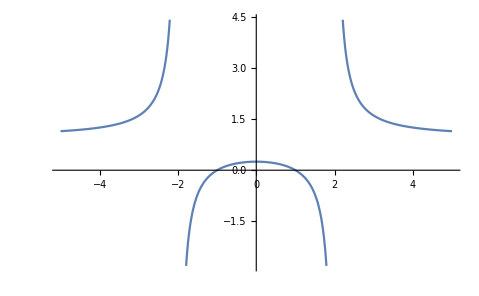

```mathematica
ClearAll[f]
f[x_]:= (x^2-1)/(x^2-4)
Plot[f[x], {x,-5,5}]
```

Določi ničle.□

```mathematica
Roots[f[x]==0,x]
```

x==1||x==-1

Določi pole in razišči obnašanje funkcije v okolici polov.

```mathematica
poli = x/.Solve[x^2== 4, x]
```

{-2,2}

```mathematica
Limit[f[x], x -> poli, Direction->"FromAbove"]
```

{-∞,∞}

```mathematica
Limit[f[x], x -> poli, Direction->"FromBelow"]
```

{∞,-∞}

Table::iterb: Iterator {i,x==2||x==-2} does not have appropriate bounds.

Izračunaj limiti v neskončnosti.
□

```mathematica
gg := {1,-1}
Limit[f[x], x->  gg ∞]
```

{1,1}

Določi stacionarne točke.

```mathematica
stacio = x /.Solve[f'[x]==0]
```

{0}

Določi vrsto stacionarnih točk (lokalni minimum, lokalni maksimum, prevoj).

```mathematica
f''[x] /.  x-> stacio
```

{-3/8}

```mathematica
O č i t n o  j e t o l o k a l n i m a k s i m u m
```

Določi intervale konveksnosti.

```mathematica
Reduce[f''[x] < 0]
```

-2<x<2

Določi intervale konkavnosti.

```mathematica
Reduce[f''[x] > 0]
```

x<-2||x>2

### 10. naloga:

Analiziraj funkcijo y=arctg x^2/(x^2-1). Zgleduj se po prejšnji nalogi.

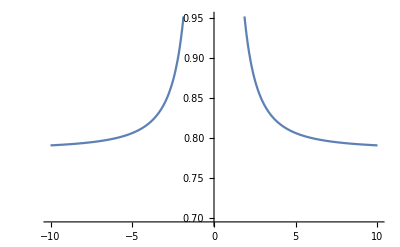

```mathematica
ClearAll[x, h]
h[x_] := ArcTan[x^2/(x^2-1)]
Plot[h[x], {x, -10,10}] // Quiet
```

### 11. naloga:

Določi tangento na funkcijo h(x)=sin^2 x-cos x  v točki x=2. Rezultat predstavi s sliko.

```mathematica
ClearAll[x,a,g,h]
h[x_] = Sin[x]^2-Cos[x]
```

-Cos[x]+Sin[x]^2

```mathematica
x1 = 2
```

2

```mathematica
k = h'[x1]
```

Sin[2]+2 Cos[2] Sin[2]

```mathematica
n = h[x1] - x1*k
```

-Cos[2]+Sin[2]^2-2 (Sin[2]+2 Cos[2] Sin[2])

```mathematica
tang[x_] = k*x + n
```

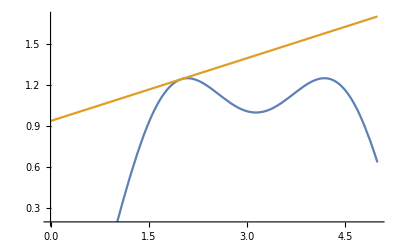

```mathematica
Plot[{h[x], tang[x]},{x,0,5}]
```

### 12. naloga:

Dana sta vektorja  (v⃗)_1=(1,2,3)  in  (v⃗)_2=(-3,-2,5). Zapiši ju kot dve spremenljivki.

```mathematica
v1 = {1,2,3}
v2 = {-3,-2,5}
```

{1,2,3}

{-3,-2,5}

Izračunaj njun skalarni produkt.

```mathematica
skala = v1.v2
```

8

Izračunaj njun vektorski produkt.

```mathematica
vect = Cross[v1,v2]
```

{16,-14,4}

Kateri od vektorjev je daljši?

```mathematica
SortBy[{v1,v2},-Norm]
```

{{-3,-2,5},{1,2,3}}

Sestavi enačbo ravnine, ki gre skozi točko (1,1,1) in ima normalo v smeri vektorskega produkta.

```mathematica
vect.{x,y,z} - vect.{1,1,1}==0
```

-6+16 x-14 y+4 z==0

### 13. naloga:

Dana je matrika  M=(9 | 2 | -3
3 | 2 | 1
6 | 4 | -1).  Zapiši jo kot spremenljivko.

```mathematica
ClearAll[m]
m = {{9,2,-3},{3,2,1},{6,4,-1}}
m // MatrixForm
```

{{9,2,-3},{3,2,1},{6,4,-1}}

(9 | 2 | -3
3 | 2 | 1
6 | 4 | -1)

Izračunaj njeno determinanto.□

```mathematica
Det[m]
```

-36

Izračunaj njene lastne vrednosti.

```mathematica
eigen = Eigenvalues[m]
```

{3 (1+√2),4,3 (1-√2)}

Izračunaj njene lastne vektorje.

```mathematica
eigenv = Eigenvectors[m]
```

{{-(-6-5 √2)/(6 (1+√2)),-(-2-√2)/(2 (1+√2)),1},{2,7,8},{-(-5+3 √2)/(3 √2 (-1+√2)),-(2-√2)/(2 (-1+√2)),1}}

Ali je matrika diagonalizabilna?

```mathematica
DiagonalizableMatrixQ[m]
```

True

Matriko želimo diagonalizirati. Konstruiraj diagonalno matriko (po diagonali ima lastne vrednosti), prehodno matriko (za stolpce ima lastne vektorje) in inverz prehodne matrike.

```mathematica
DiagonalMatrix[m]
```

DiagonalMatrix::vector: Argument {{9,2,-3},{3,2,1},{6,4,-1}} at position 1 is not a non-empty vector.

```mathematica
DiagonalMatrix[Eigenvalues[m]] // MatrixForm
eigenv
```

(3 (1+√2) | 0 | 0
0 | 4 | 0
0 | 0 | 3 (1-√2))

{{-(-6-5 √2)/(6 (1+√2)),-(-2-√2)/(2 (1+√2)),1},{2,7,8},{-(-5+3 √2)/(3 √2 (-1+√2)),-(2-√2)/(2 (-1+√2)),1}}

```mathematica
prehodna = {{eigenv[[1]][[1]],eigenv[[2]][[1]],eigenv[[3]][[1]]},{eigenv[[1]][[2]],eigenv[[2]][[2]],eigenv[[3]][[2]]},{eigenv[[1]][[3]],eigenv[[2]][[3]],eigenv[[3]][[3]]}
}
```

{{-(-6-5 √2)/(6 (1+√2)),2,-(-5+3 √2)/(3 √2 (-1+√2))},{-(-2-√2)/(2 (1+√2)),7,-(2-√2)/(2 (-1+√2))},{1,8,1}}

```mathematica
Inverse[prehodna]
```

{{(7+8/(-1+√2)-(4 √2)/(-1+√2))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(-2-8/(-1+√2)+(20 √2)/(3 (-1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(5/(-1+√2)-29/(3 √2 (-1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2)))},{(-1/(-1+√2)+1/(√2 (-1+√2))-1/(1+√2)-1/(√2 (1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(1/(-1+√2)-5/(3 √2 (-1+√2))+1/(1+√2)+5/(3 √2 (1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(2 √2)/(3 (-1+√2) (1+√2) (5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))))},{(-7+8/(1+√2)+(4 √2)/(1+√2))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(2-8/(1+√2)-(20 √2)/(3 (1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(5/(1+√2)+29/(3 √2 (1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2)))}}

```mathematica
DiagonalizableMatrixQ[Inverse[prehodna]]
```

True

Preveri, ali velja pogoj za diagonalizabilnost.

### 14. naloga:

Dana je parametrično podana krivulja  (((3-t) sin t)/(t+1),cos (t) sin (2t)). Definiraj jo kot funkcijo ene spremenljivke.

```mathematica
ClearAll[f,k]
```

```mathematica
f[t_] = {(3-t)Sin[t]/(t+1), Cos[t]Sin[2t]};
```

```mathematica
ParametricPlot[f[t],{t,0,5}]
```

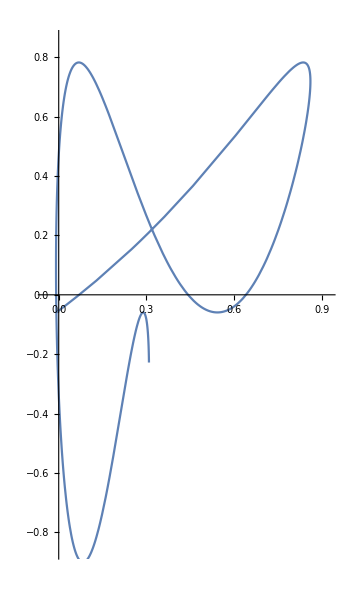

Nariši krivuljo za  t∈[0,5].

Krivulja seče samo sebe natanko dvakrat. S pomočjo numeričnega reševanja enačb (FindRoot) poišči približek presečišč. Enačbo nastavi tako da izenačiš krivuljo, parametrizirano s parametrom t, s krivuljo, parametrizirano s parametrom s. Potem s spreminjanjem začetnih približkov parametrov t in s poskusi določiti vrednosti parametrov, pri katerih pride do samopresečič.

Iz dobljenih rešitev sestavi točki.

Grafično preveri, ali gre za pravilen izračun.

### 15. naloga:

Naj bodo a⃗, b⃗ in c⃗ vektorji v R^3.
S simboličnim računom dokaži identiteto  a⃗×(b⃗×c⃗)=(a⃗·c⃗)b⃗-(a⃗·b⃗)c⃗

### 16. naloga:

Dokaži, da za poljubni 2×2 matriki A in B velja enakost  (A B)^-1=B^-1 A^-1.